```mathematica
PXaY[tota_]:=Catch[Module[{tang=tota,labor,fruit={0,0}},
labor=Floor[1/2 (-1+Sqrt[-7+8 tang])];
fruit[[1]]=tang-1/2 labor (1+labor);
labor=Ceiling[1/2 (-1+Sqrt[1+8 tang])];
fruit[[2]]=1/2(2-2tang+labor+labor^2);
Throw[fruit];
]];

Pxy[toA_]:=Catch[Module[{toar=toA,lbr1={0,0},lbr2},
If[Length[toar]==0,Throw[PXaY[toar]];];
If[Length[toar]==1,Throw[PXaY[toar[[1]]]];];
If[Length[toar]==2,Goto["SPnt1"],Throw["Invalid Input"];];
Label["SPnt1"];
lbr1=toar;
lbr2=lbr1[[1]]+lbr1[[2]];
lbr2=(lbr2(lbr2-1))/2-lbr1[[2]]+1;
Throw[lbr2];
]];

TaT[TaT1_]:=Catch[Module[{TTa1=TaT1,TTa2a,TTa2b=0,mem={0,0},set=2},
TTa2a=TTa1;
Label["SPnt1"];
mem[[1]]=Mod[TTa2a,set];
mem[[1]]=If[mem[[1]]==0,set,mem[[1]]];
mem[[2]]=If[mem[[1]]==0,1,0];
TTa2b++;
TTa2a=Quotient[TTa2a,set]-mem[[2]];
If[TTa2a≤0,Throw[TTa2b];,set=If[set==2,3,2];Goto["SPnt1"];];

]];

TaT2[TaT1_]:=Catch[Module[{TTa1=TaT1,TTa2a,TTa2b=0,mem={0,0},set=2},
TTa2a=TTa1;
Label["SPnt1"];
mem[[1]]=Mod[TTa2a,set];
mem[[1]]=If[mem[[1]]==0,set,mem[[1]]];
mem[[2]]=If[mem[[1]]==0,1,0];
TTa2b=TTa2b+mem[[1]];
TTa2a=Quotient[TTa2a,set]-mem[[2]];
If[TTa2a≤0,Throw[TTa2b];,set=If[set==2,3,2];Goto["SPnt1"];];

]];

"The Main Fundctions which enable this technique"
```

The Main Fundctions which enable this technique

```mathematica
PTInI[inty_,inty2_]:=Catch[Module[{rg1=inty,rex=inty2,mem={0,0,0,0,0},dat={},cnt=0},
mem[[5]]=Floor[Pxy[{rg1,rex[[1]]}]];
mem[[1]]=(TaT2[mem[[5]]])TaT[mem[[5]]]rex[[2]];
mem[[2]]=Floor[√mem[[5]]];
mem[[3]]=Floor[Pxy[{mem[[5]] TaT2[mem[[5]]rex[[3]] ]rex[[2]],1}]/(((mem[[5]]+1)mem[[5]])/2)];
Label["Testing"];
cnt++;
If[mem[[3]]≤0,Throw[{"Failed",dat}]; Break[];];
mem[[3]]=mem[[3]]-mem[[1]];
mem[[4]]=mem[[3]]-Mod[mem[[3]],2]-1;
dat=Append[dat,mem[[4]]];
Throw[mem[[4]]];
Goto["Testing"];
]];

"If You change the lower factor you will notice the distortion shifts this shows the user where they should look for their factor and gives a clue as to the bounds in which the co-prime is in"
```

If You change the lower factor you will notice the distortion shifts this shows the user where they should look for their factor and gives a clue as to the bounds in which the co-prime is in

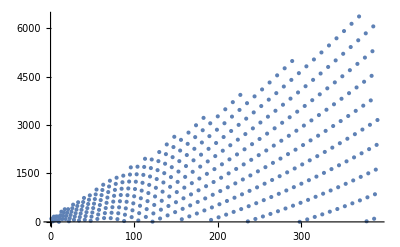

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[70],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

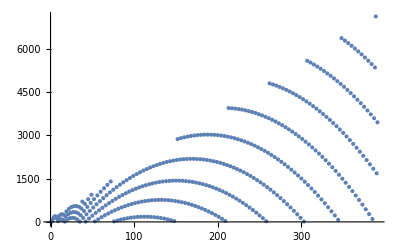

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[7000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

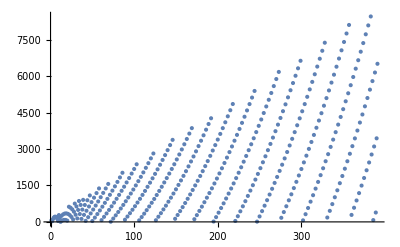

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[70000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

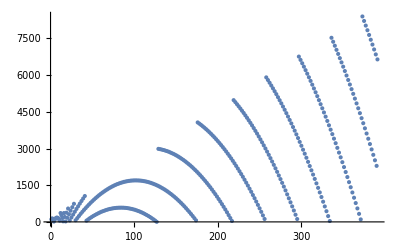

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[700000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

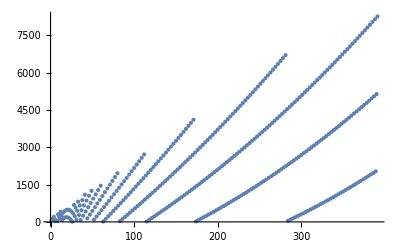

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[7000000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

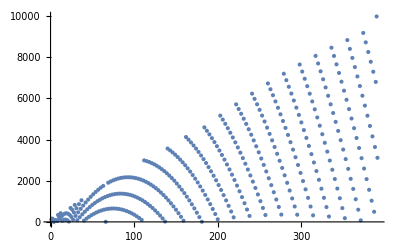

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000000]Prime[70000000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

```mathematica
"Ok So now I'm going to measure as my larger factor prime[1000000] to show how the distortion thing is similar.
"
```

Ok So now I'm going to measure as my larger factor prime[1000000] to show how the distortion thing is similar.

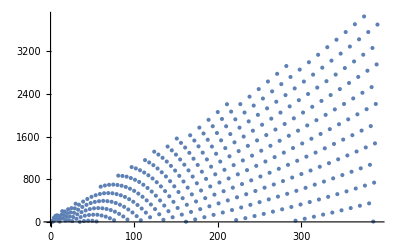

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[7],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

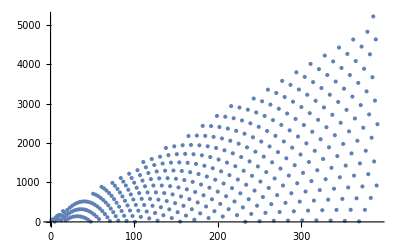

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[70],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

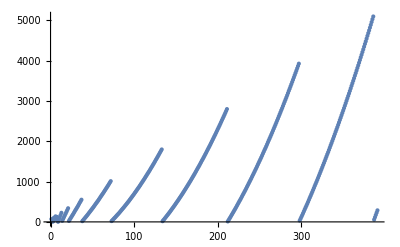

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[700],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

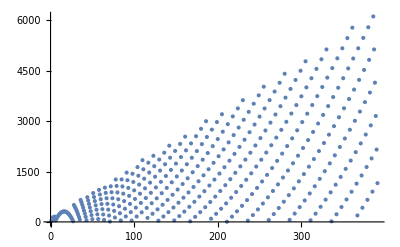

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[7000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

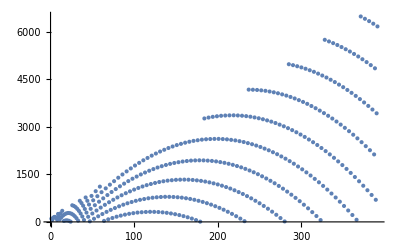

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[70000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

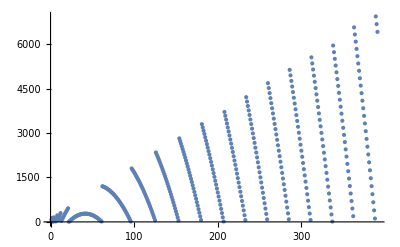

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[700000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

```mathematica
"Now lets see what happens with 3 prime composites"
```

Now lets see what happens with 3 prime composites

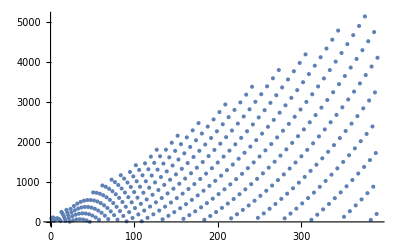

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[7]Prime[14],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

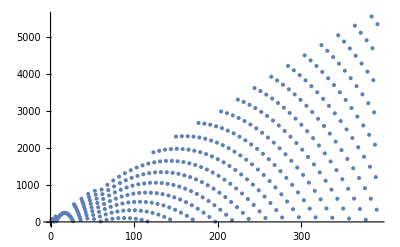

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[70]Prime[40],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

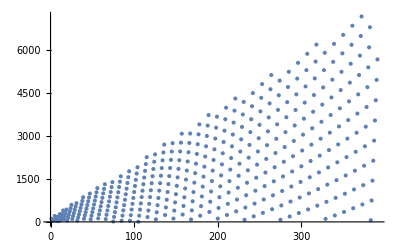

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[700]Prime[400],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

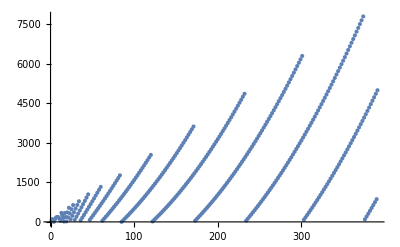

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[7000]Prime[4000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

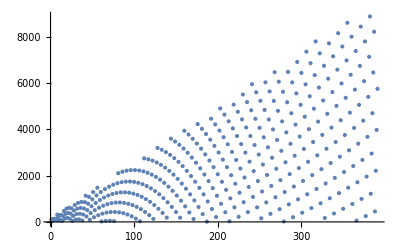

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[70000]Prime[40000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```

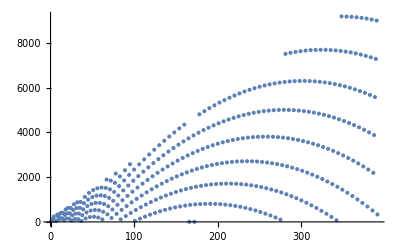

```mathematica
ListPlot[Table[PXaY[PTInI[Prime[1000000]Prime[700000]Prime[400000],{1,yy1,1}]][[1]],{yy1,1,40,0.1}]]
```